```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];
```

Suffix: hT

Sample sizes: 10000

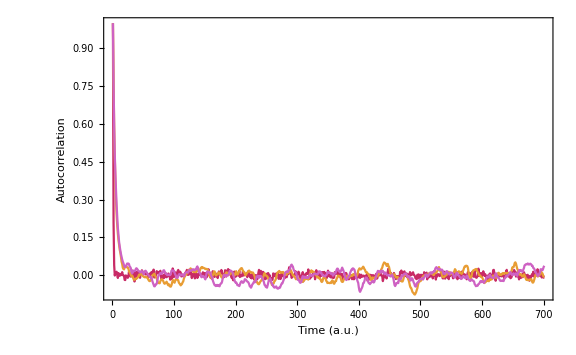

```mathematica
{engyMc, engyA1,engyA2} =#["energy_sample"]&/@{mcData, a1Data,a2Data};

Row@{"Sample sizes: ",sampleSize=Length[engyMc]}
Assert@And[
sampleSize==Length[engyA1],
sampleSize==Length[engyA2]
] 
colors = Table[ColorData[54][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->16];
frameStyle = Append[baseStyle, Thickness@0.003];

ListLinePlot[
CorrelationFunction[#["energy_sample"], {700}]& /@{mcData, a1Data, a2Data},
PlotRange->All,
PlotStyle->colors,
FrameLabel->{
{"Autocorrelation",None},{"Time (a.u.)",None}
},
FrameTicksStyle->Thickness@0.003,
Epilog->{
Inset[Framed[
SwatchLegend[colors,
{"Mc","A1","A2"},
LegendLayout->"Row",LabelStyle->baseStyle
],FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5
],Scaled@{0.8,0.8}]
},

BaseStyle->baseStyle,
Axes->False,Frame->True,FrameStyle->Append[baseStyle,Thickness@0.004],
ImageSize->Large
]
```